4.8: 14, 26

```mathematica
newtonNext[f_,x_]:=SetPrecision[x-f[x]/f'[x],10];
nm[f_,x0_?NumberQ,steps_?NumberQ]:=
Module[
{i=0,x=SetPrecision[x0,10]}, 
While[i<steps,
Print[{i,x,f[x]}]; 
x=newtonNext[f,x];i++]];
```

14: Approximate the root of the following function in [-2,-1] to six decimal places.

```mathematica
f[x_]:=2.2x^5-4.4x^3+1.3x^2-0.9x-4.0
```

```mathematica
nm[f,-1.5,10]
```

{0,-1.5,-1.58125}

{1,-1.425368732,-0.277796}

{2,-1.405498787,-0.0168981}

{3,-1.404124452,-0.0000777729}

{4,-1.404118068,-1.67378×10^-9}

{5,-1.404118068,-2.22045×10^-15}

{6,-1.404118068,1.77636×10^-15}

{7,-1.404118068,-2.22045×10^-15}

{8,-1.404118068,1.77636×10^-15}

{9,-1.404118068,-2.22045×10^-15}

I applied Newton’s method with 10 iterations and a starting guess of x0=-1.5. It appears that the/a root in the interval [-2,-1] is -1.404118068.

26: Find all roots of the following equation correct to eight decimal places:

```mathematica
3Sin[x^2] == 2x;
```

```mathematica
g[x_]:=3Sin[x^2] - 2x
```

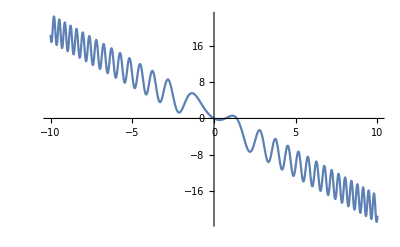

```mathematica
Plot[g[x],{x,-10,10}]
```

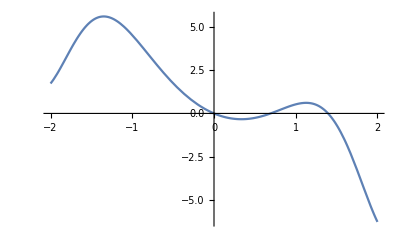

```mathematica
Plot[g[x],{x,-2,2}]
```

It appears that there are solutions at x=0 (this is clear), near 0.6 and near 1.2. Let’s take a look:

```mathematica
nm[g,0.6,10]
```

{0,0.6,-0.1431773}

{1,0.7045678595,0.01969557}

{2,0.6930978706,0.00016525}

{3,0.6929999667,1.×10^-8}

{4,0.6929999592,0.}

{5,0.6929999592,0.}

{6,0.6929999592,0.}

{7,0.6929999592,0.}

{8,0.6929999592,0.}

{9,0.6929999592,0.}

Yep, so one solution is at 0.6929999592.

```mathematica
nm[g,1.2,10]
```

{0,1.2,0.574375045}

{1,1.741378411,-3.15582576}

{2,1.48658956,-0.56537379}

{3,1.409359452,-0.07397233}

{4,1.395694499,-0.00225361}

{5,1.395251233,-2.35×10^-6}

{6,1.39525077,0.}

{7,1.39525077,0.}

{8,1.39525077,0.}

{9,1.39525077,0.}

And the final solution is at 1.395250770.